# Solow Growth Model:

## Hipóteses:

Principal conclui que a a vasta acumulação  de capital não  pode explicar a disparidade  da produção per capta.

Modelo não tem otimização, leva em conta a taxa de poupança como exógena]

Hipóteses acerca da trajetória do estoque de trabalho (L), conhecimento ou técnologia  (A) e capital.:

tecnologia e trabalho crescem a taxas constantes:

Função de produção homogenea de grau 1 ( F[cAL,cK] == c(F[AL,K]);  supondo c=1/AL

F[AL/AL,K/AL = F[1,K/AL]   -⟶ K/AL capital por unidade  efetiva de trabalho

### Dinâmica do capital ( k̇ = sf(k) - (n+g+δ) k(t):

```mathematica
F[z_,s_,a_,d_,n_,g_] := s*(z^a)-(n+g+d)*z
```

```mathematica
z̄= (s/(d+n+g))^(1/(1-a))
```

(s/(d+g+n))^(1/(1-a))

testando com alpha1  =0.69 a velocidade de convergencua e alpha2=0.33

```mathematica
Subscript[a, 1]= 0.59 ; Subscript[a, 2] = 0.33; n = 0.01
d =0.03 ; g =0.02 ; s = 0.25

zs1 =(s/(g+n+d))^(1/(1-Subscript[a, 1]))
zs2 = (s/(g+n+d))^(1/(1-Subscript[a, 2]))
```

0.01

0.25

32.4848

8.41507

agora vamos resolver para z’[t]

```mathematica
sol1 = NDSolve[{z'[t]== F[z[t],0.25,0.69,0.03,0.01,0.02], z[0] == zs1/2}, z, {t,0,200}]
sol2 = NDSolve[{z'[t]== F[z[t],0.25,0.33,0.03,0.01,0.02], z[0] == zs2/2}, z, {t,0,200}]
```

{{z→InterpolatingFunction[…]}}

{{z→InterpolatingFunction[…]}}

```mathematica
pz1[t_]:=z[t]/.sol1
pz2[t_]:=z[t]/.sol2
```

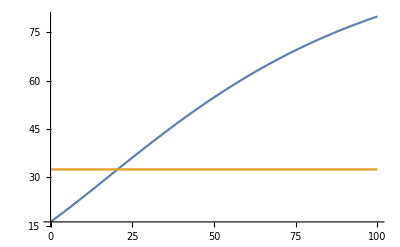

```mathematica
Plot[{pz1[t],zs1},{t,0,100}]
```

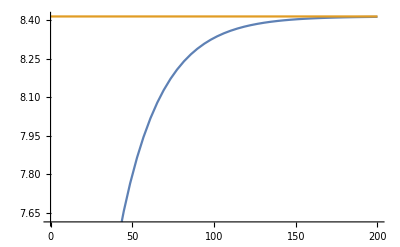

```mathematica
Plot[{pz2[t],zs2},{t,0,200}]
```